# “One size fits all” analytic solutions to the Grad–Shafranov equation

Physics of Plasmas 17, 032502 (2010); https://doi.org/10.1063/1.3328818
Antoine J. Cerfona) and Jeffrey P. Freidberg

```mathematica
Clear["Global`*"]
Needs["Notation`"]
Symbolize[ParsedBoxWrapper[SubscriptBox["_","_"]]];
Symbolize[ParsedBoxWrapper[SubsuperscriptBox["_","_","_"]]];
```

### Define here the basic physical quantities of your equilibrium:

```mathematica
Subscript[m, p]=1.67262178*10^-27;Subscript[m, n]=1.674927351*10^-27;Subscript[m, e]=9.1093829140*10^-31;e=1.60217657×10^-19;Subscript[ϵ, 0]=8.85418782*10^-12;lnΛ=12;Subscript[T, e]=1.58*1000*e;Subscript[T, i]=0.27*1000*e;
Subscript[m, d]=Subscript[m, n]+Subscript[m, p];Subscript[m, t]=2*Subscript[m, n]+Subscript[m, p];
Quantities={"Name","Shot","R_0[m]","Z_0[m]","R_(0, mag)[m]","Z_(0, mag)[m]","R_(,sep)[m]","Z_Sep[m]","a","ϵ (inverse aspect ratio)","κ (elongation)","δ (triangularity)","B_0[T]","T_(e, ref)[eV]","n_(e, ref)[m^-3]","m_(i, ref)[kg]"};
ITER={"ITER","basleline",6.2,0,6.2,0,0,0,2,2/6.2,1.7,0.33,5.3,500e,6.*10^19,Subscript[m, d]};
JET={"JET","86470@t=54.9884s",2.9094,0.214839,2.97825,0.383874,2.69366,-1.32142-0.214839,0.905198,0.905198/2.9094,1.69607,0.238282,3.45,500e,6.*10^19,Subscript[m, d]};
AUG={"AUG","fantasy",1.65,0,1.65,0,0,0,0.5,0.5/1.65,1.7,0.33,2,50e,6.*10^19,Subscript[m, d]};(*update*)
COMPASS={"COMPASS",9435,0.557,0,0.557,0,0,0,0.232,0.232/0.557,1.6594,0.4,1.2,200e,6.*10^19,Subscript[m, d]};(*Subscript[B, 0]=0.8-2.1 T*)
COMPASS={"COMPASS","fantasy",0.56,0,0.56,0,0,0,0.2,0.2/0.56,1.6594,0.4,0.8,300e,8.*10^19,Subscript[m, d]};(*small ref with some parameters of L mode 9435*)
TJK={"TJK","fantasy",0.557,0,0.557,0,0,0,0.23,0.232/0.557,1.75,0.47,1,50e,6.*10^19,Subscript[m, d]};(*update*)
TCV={"TCV","fantasy",0.89,0,0.89,0,0,0,0.25,0.25/0.89,1.6,-0.4,1.44,500e,1.43*10^19,Subscript[m, d]};(*update*)
AlcatorCmod={"AlcatorCmod","fantasy",0.68,0,0.68,0,0,0,0.22,0.22/0.68,1.75,0.47,2.6,50e,6.*10^19,Subscript[m, d]};(*Subscript[B, 0]=2.6-8 T*)
START={"START","fantasy",0.32,0,0.32,0,0,0,0.27,0.27/0.32,1.75,0.47,0.31,150e,6.*10^19,Subscript[m, d]};(*update*)
MAST={"MAST","fantasy",0.85,0,0.85,0,0,0,0.65,0.65/0.85,1.75,0.47,0.52,50e,6.*10^19,Subscript[m, d]};(*update*)
MASTU={"MASTU","fantasy",0.85,0,0.85,0,0,0,0.65,0.65/0.85,1.75,0.47,1,50e,6.*10^19,Subscript[m, d]};(*update*)
NSTX={"NSTX","fantasy",0.85,0,0.85,0,0,0,0.68,0.68/0.85,1.75,0.47,0.6,50e,6.*10^19,Subscript[m, d]};(*update*)
NSTXU={"NSTXU","fantasy",0.85,0,0.85,0,0,0,0.68,0.68/0.85,1.75,0.47,1,50e,6.*10^19,Subscript[m, d]};(*update*)
ST25={"ST25","fantasy",0.25,0,0.25,0,0,0,0.23,0.23/0.25,1.75,0.47,0.1,50e,6.*10^19,Subscript[m, d]};(*update*)
ST40={"ST40","fantasy",0.4,0,0.4,0,0,0,0.22,0.22/0.4,2.6,0.47,3,200e,6.*10^19,Subscript[m, d]};(*Subscript[B, 0]=~1-3T*)
ST135={"ST25","fantasy",1.35,0,1.35,0,0,0,0.75,0.75/1.35,2.64,0.47,3.7,50e,6.*10^19,Subscript[m, d]};(*update*)
FRC={"FRC","fantasy",0.4,0,0.4,0,0,0,0.4,0.4,1,1,0.6,50,6.*10^19,Subscript[m, d]};(*C-2 of TAE*)
Grid[Transpose[{Quantities,ITER,JET,AUG,COMPASS,TCV,TJK,START,MAST,NSTX,ST25,ST40,FRC}],Alignment->Left,Frame->All,Background->{{{LightBlue,None}},{{LightGray,None}}}]
```

Name | ITER | JET | AUG | COMPASS | TCV | TJK | START | MAST | NSTX | ST25 | ST40 | FRC
Shot | basleline | 86470@t=54.9884s | fantasy | fantasy | fantasy | fantasy | fantasy | fantasy | fantasy | fantasy | fantasy | fantasy
R_0[m] | 6.2 | 2.9094 | 1.65 | 0.56 | 0.89 | 0.557 | 0.32 | 0.85 | 0.85 | 0.25 | 0.4 | 0.4
Z_0[m] | 0 | 0.214839 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
R_(0, mag)[m] | 6.2 | 2.97825 | 1.65 | 0.56 | 0.89 | 0.557 | 0.32 | 0.85 | 0.85 | 0.25 | 0.4 | 0.4
Z_(0, mag)[m] | 0 | 0.383874 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
R_(,sep)[m] | 0 | 2.69366 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Z_Sep[m] | 0 | -1.53626 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
a | 2 | 0.905198 | 0.5 | 0.2 | 0.25 | 0.23 | 0.27 | 0.65 | 0.68 | 0.23 | 0.22 | 0.4
ϵ (inverse aspect ratio) | 0.322581 | 0.311129 | 0.30303 | 0.357143 | 0.280899 | 0.416517 | 0.84375 | 0.764706 | 0.8 | 0.92 | 0.55 | 0.4
κ (elongation) | 1.7 | 1.69607 | 1.7 | 1.6594 | 1.6 | 1.75 | 1.75 | 1.75 | 1.75 | 1.75 | 2.6 | 1
δ (triangularity) | 0.33 | 0.238282 | 0.33 | 0.4 | -0.4 | 0.47 | 0.47 | 0.47 | 0.47 | 0.47 | 0.47 | 1
B_0[T] | 5.3 | 3.45 | 2 | 0.8 | 1.44 | 1 | 0.31 | 0.52 | 0.6 | 0.1 | 3 | 0.6
T_(e, ref)[eV] | 8.01088×10^-17 | 8.01088×10^-17 | 8.01088×10^-18 | 4.80653×10^-17 | 8.01088×10^-17 | 8.01088×10^-18 | 2.40326×10^-17 | 8.01088×10^-18 | 8.01088×10^-18 | 8.01088×10^-18 | 3.20435×10^-17 | 50
n_(e, ref)[m^-3] | 6.×10^19 | 6.×10^19 | 6.×10^19 | 8.×10^19 | 1.43×10^19 | 6.×10^19 | 6.×10^19 | 6.×10^19 | 6.×10^19 | 6.×10^19 | 6.×10^19 | 6.×10^19
m_(i, ref)[kg] | 3.34755×10^-27 | 3.34755×10^-27 | 3.34755×10^-27 | 3.34755×10^-27 | 3.34755×10^-27 | 3.34755×10^-27 | 3.34755×10^-27 | 3.34755×10^-27 | 3.34755×10^-27 | 3.34755×10^-27 | 3.34755×10^-27 | 3.34755×10^-27

### Compute normalized quantities (in terms of rho_s,etc. and plot boundary curve of device for fit

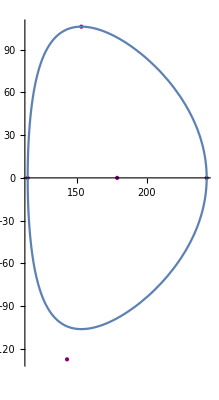

```mathematica
{Device,Shot,Subscript[R, 0],Subscript[Z, 0],Subscript[R, 0,mag],Subscript[Z, 0,mag],Subscript[R, sep],Subscript[Z, sep],a,ϵ,κ,δ,Subscript[B, 0],Subscript[T, e],Subscript[n, e],Subscript[m, i]}=COMPASS[[1;;]];
α=ArcSin[δ];
Subscript[ρ, s]=Sqrt[Subscript[T, e](Subscript[m, d])]/(e*Subscript[B, 0]);
(*reset X-point  to good value if (0,0)*)
If[Subscript[R, sep]==0&&Subscript[Z, sep]==0,If[δ>0,Subscript[R, sep]=Subscript[R, 0]-1.4*δ*a;Subscript[Z, sep]=-1.2*κ*a;,Subscript[R, sep]=Subscript[R, 0]-1.6*δ*a;Subscript[Z, sep]=-1.2*κ*a;],];
Subscript[ν, e]=(3*(2*π)^(3/2)((Subscript[ϵ, 0])^2(Subscript[m, e])^(1/2)(Subscript[T, e])^(3/2))/(Subscript[n, e] e^4 lnΛ*Subscript[Z, i]^2))^-1;
(*(*normalize with Subscript[ρ, s] ->h and Subscript[R, 0] ->b*)*)
Subscript[R, 0h]=Subscript[R, 0]/Subscript[ρ, s];
Subscript[a, h]=a/Subscript[ρ, s];
Subscript[R, seph]=Subscript[R, sep]/Subscript[ρ, s];Subscript[Z, seph]=Subscript[Z, sep]/Subscript[ρ, s];
pointsX={{Subscript[R, 0h],0},{Subscript[R, 0h]+Subscript[a, h],0},{Subscript[R, 0h]-Subscript[a, h],0},{Subscript[R, 0h]-δ*Subscript[a, h],κ*Subscript[a, h]},{Subscript[R, seph],Subscript[Z, seph]}};
Subscript[R, minh]=Subscript[R, 0h]-1.2*Subscript[a, h];Subscript[R, maxh]=Subscript[R, 0h]+1.8*Subscript[a, h];Subscript[Z, minh]=-κ*Subscript[a, h] 1.4;Subscript[Z, maxh]=κ*Subscript[a, h] 1.2;
Subscript[μ, 0]=4*π*10^-7;(*N/A^2*)
(*normalize with Subscript[ρ, s] and Subscript[R, 0]*)
Subscript[I, 0h]=Subscript[B, 0] Subscript[R, 0];(*in SI*)
Subscript[ψ, p0h]=Subscript[ρ, s] Subscript[B, 0] Subscript[R, 0];(*in SI*)
Subscript[p, 0h]=Subscript[ψ, p0h]^2/(Subscript[μ, 0] Subscript[ρ, s]^4);(*in SI*)
Subscript[j, φ0h]=Subscript[ψ, p0h]/(Subscript[μ, 0] Subscript[ρ, s]^3);(*in SI*)
Subscript[I, 0b]=Subscript[B, 0] Subscript[R, 0];(*in SI*)
Subscript[ψ, p0b]=Subscript[B, 0] Subscript[R, 0]^2;(*= Subscript[B, 0] Subscript[R, 0]^2 ... in SI*)
Subscript[p, 0b]=Subscript[ψ, p0b]^2/(Subscript[μ, 0] Subscript[R, 0]^4);
Subscript[j, φ0b]=Subscript[ψ, p0b]/(Subscript[μ, 0] Subscript[R, 0]^3);
(*Make parametric tokamak plot*)
(*parametric curve*)
If[Device=="FRC",
Subscript[R, ph]=Function[{τ},(Subscript[R, 0h]+Subscript[a, h])Cos[τ]//Evaluate];
Subscript[Z, ph]=Function[{τ},Subscript[R, 0h] κ*Sin[τ]//Evaluate];
Show[{ParametricPlot[{Subscript[R, ph][τ],Subscript[Z, ph][τ]},{τ,0,2π}]},AspectRatio->Automatic,PlotRange->All],
Subscript[R, ph]=Function[{τ},Subscript[R, 0h]+Subscript[a, h]*Cos[τ+α*Sin[τ]]//Evaluate];
Subscript[Z, ph]=Function[{τ},Subscript[a, h]*κ*Sin[τ]//Evaluate];
Show[{ListPlot[pointsX,PlotStyle->Directive[PointSize[Large],Purple]],ParametricPlot[{Subscript[R, ph][τ],Subscript[Z, ph][τ]},{τ,0,2π}]},AspectRatio->Automatic,PlotRange->All]
]
```

### Here, we define the solov’ev solution:

```mathematica
Subscript[ψ, 1b]=Function[{Subscript[R, b],Subscript[Z, b]},1//Evaluate];
Subscript[ψ, 2b]=Function[{Subscript[R, b],Subscript[Z, b]},Subscript[R, b]^2//Evaluate];
Subscript[ψ, 3b]=Function[{Subscript[R, b],Subscript[Z, b]},Subscript[Z, b]^2-Subscript[R, b]^2 Log[Subscript[R, b]]//Evaluate];
Subscript[ψ, 4b]=Function[{Subscript[R, b],Subscript[Z, b]},Subscript[R, b]^4-4*Subscript[R, b]^2 Subscript[Z, b]^2//Evaluate];
Subscript[ψ, 5b]=Function[{Subscript[R, b],Subscript[Z, b]},2 Subscript[Z, b]^4-9 Subscript[Z, b]^2 Subscript[R, b]^2+3 Subscript[R, b]^4 Log[Subscript[R, b]]-12 Subscript[R, b]^2 Subscript[Z, b]^2 Log[Subscript[R, b]]//Evaluate];
Subscript[ψ, 6b]=Function[{Subscript[R, b],Subscript[Z, b]},Subscript[R, b]^6-12 Subscript[R, b]^4 Subscript[Z, b]^2+8 Subscript[R, b]^2 Subscript[Z, b]^4//Evaluate];
Subscript[ψ, 7b]=Function[{Subscript[R, b],Subscript[Z, b]},8 Subscript[Z, b]^6-140 Subscript[Z, b]^4 Subscript[R, b]^2+75 Subscript[Z, b]^2 Subscript[R, b]^4-15 Subscript[R, b]^6 Log[Subscript[R, b]]+180 Subscript[R, b]^4 Subscript[Z, b]^2 Log[Subscript[R, b]]-120 Subscript[R, b]^2 Subscript[Z, b]^4 Log[Subscript[R, b]]//Evaluate];
Subscript[ψ, 8b]=Function[{Subscript[R, b],Subscript[Z, b]},Subscript[Z, b]//Evaluate];
Subscript[ψ, 9b]=Function[{Subscript[R, b],Subscript[Z, b]},Subscript[Z, b]*Subscript[R, b]^2//Evaluate];
Subscript[ψ, 10b]=Function[{Subscript[R, b],Subscript[Z, b]},Subscript[Z, b]^3-3*Subscript[Z, b]*Subscript[R, b]^2*Log[Subscript[R, b]]//Evaluate];
Subscript[ψ, 11b]=Function[{Subscript[R, b],Subscript[Z, b]},3 Subscript[Z, b]*Subscript[R, b]^4-4*Subscript[Z, b]^3 Subscript[R, b]^2//Evaluate];
Subscript[ψ, 12b]=Function[{Subscript[R, b],Subscript[Z, b]},8 Subscript[Z, b]^5-45 Subscript[Z, b]*Subscript[R, b]^4-80*Subscript[Z, b]^3*Subscript[R, b]^2 Log[Subscript[R, b]]+60 Subscript[Z, b]*Subscript[R, b]^4 Log[Subscript[R, b]]//Evaluate];
Subscript[ψ, b]=Function[{Subscript[R, b],Subscript[Z, b],A,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],Subscript[c, 8],Subscript[c, 9],Subscript[c, 10],Subscript[c, 11],Subscript[c, 12]},(Subscript[R, b]^4/8+A(1/2 Subscript[R, b]^2 Log[Subscript[R, b]]-Subscript[R, b]^4/8)+Subscript[c, 1] Subscript[ψ, 1b][Subscript[R, b],Subscript[Z, b]]+Subscript[c, 2] Subscript[ψ, 2b][Subscript[R, b],Subscript[Z, b]]+Subscript[c, 3] Subscript[ψ, 3b][Subscript[R, b],Subscript[Z, b]]+Subscript[c, 4] Subscript[ψ, 4b][Subscript[R, b],Subscript[Z, b]]+Subscript[c, 5] Subscript[ψ, 5b][Subscript[R, b],Subscript[Z, b]]+Subscript[c, 6] Subscript[ψ, 6b][Subscript[R, b],Subscript[Z, b]]+Subscript[c, 7] Subscript[ψ, 7b][Subscript[R, b],Subscript[Z, b]]+Subscript[c, 8] Subscript[ψ, 8b][Subscript[R, b],Subscript[Z, b]]+Subscript[c, 9] Subscript[ψ, 9b][Subscript[R, b],Subscript[Z, b]]+Subscript[c, 10] Subscript[ψ, 10b][Subscript[R, b],Subscript[Z, b]]+Subscript[c, 11] Subscript[ψ, 11b][Subscript[R, b],Subscript[Z, b]]+Subscript[c, 12] Subscript[ψ, 12b][Subscript[R, b],Subscript[Z, b]])//Evaluate];
Subscript[p, b]=Function[{Subscript[R, b],Subscript[Z, b],A,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],Subscript[c, 8],Subscript[c, 9],Subscript[c, 10],Subscript[c, 11],Subscript[c, 12]},(A-1)Subscript[ψ, b][Subscript[R, b],Subscript[Z, b],A,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],Subscript[c, 8],Subscript[c, 9],Subscript[c, 10],Subscript[c, 11],Subscript[c, 12]]//Evaluate];
Subscript[j, φb]=Function[{Subscript[R, b],A},((A-1)Subscript[R, b]-A/Subscript[R, b])//Evaluate];(*in units*)
Subscript[F, b]^2=Function[{Subscript[R, b],Subscript[Z, b],A,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],Subscript[c, 8],Subscript[c, 9],Subscript[c, 10],Subscript[c, 11],Subscript[c, 12]},-2*A*(Subscript[ψ, b][Subscript[R, b],Subscript[Z, b],A,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],Subscript[c, 8],Subscript[c, 9],Subscript[c, 10],Subscript[c, 11],Subscript[c, 12]])+1^2//Evaluate];
Subscript[F, b]=Function[{Subscript[R, b],Subscript[Z, b],A,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],Subscript[c, 8],Subscript[c, 9],Subscript[c, 10],Subscript[c, 11],Subscript[c, 12]},Sqrt[(Subscript[F, b]^2)[Subscript[R, b],Subscript[Z, b],A,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],Subscript[c, 8],Subscript[c, 9],Subscript[c, 10],Subscript[c, 11],Subscript[c, 12]]]//Evaluate];
Subscript[B, tb]^2=Function[{Subscript[R, b],Subscript[Z, b],A,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],Subscript[c, 8],Subscript[c, 9],Subscript[c, 10],Subscript[c, 11],Subscript[c, 12]},(Subscript[F, b]^2)[Subscript[R, b],Subscript[Z, b],A,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],Subscript[c, 8],Subscript[c, 9],Subscript[c, 10],Subscript[c, 11],Subscript[c, 12]]/Subscript[R, b]^2//Evaluate];
Subscript[ψ, bR]=Function[{Subscript[R, b],Subscript[Z, b],A,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],Subscript[c, 8],Subscript[c, 9],Subscript[c, 10],Subscript[c, 11],Subscript[c, 12]},D[Subscript[ψ, b][Subscript[R, b],Subscript[Z, b],A,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],Subscript[c, 8],Subscript[c, 9],Subscript[c, 10],Subscript[c, 11],Subscript[c, 12]],{Subscript[R, b],1}]//Evaluate];
Subscript[ψ, bZ]=Function[{Subscript[R, b],Subscript[Z, b],A,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],Subscript[c, 8],Subscript[c, 9],Subscript[c, 10],Subscript[c, 11],Subscript[c, 12]},D[Subscript[ψ, b][Subscript[R, b],Subscript[Z, b],A,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],Subscript[c, 8],Subscript[c, 9],Subscript[c, 10],Subscript[c, 11],Subscript[c, 12]],{Subscript[Z, b],1}]//Evaluate];
Subscript[B, pb]^2=Function[{Subscript[R, b],Subscript[Z, b],A,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],Subscript[c, 8],Subscript[c, 9],Subscript[c, 10],Subscript[c, 11],Subscript[c, 12]},((Subscript[ψ, bR][Subscript[R, b],Subscript[Z, b],A,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],Subscript[c, 8],Subscript[c, 9],Subscript[c, 10],Subscript[c, 11],Subscript[c, 12]])^2+(Subscript[ψ, bZ][Subscript[R, b],Subscript[Z, b],A,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],Subscript[c, 8],Subscript[c, 9],Subscript[c, 10],Subscript[c, 11],Subscript[c, 12]])^2)/Subscript[R, b]^2//Evaluate];
Subscript[B, b]=Function[{Subscript[R, b],Subscript[Z, b],A,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],Subscript[c, 8],Subscript[c, 9],Subscript[c, 10],Subscript[c, 11],Subscript[c, 12]},Sqrt[(Subscript[B, pb]^2)[Subscript[R, b],Subscript[Z, b],A,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],Subscript[c, 8],Subscript[c, 9],Subscript[c, 10],Subscript[c, 11],Subscript[c, 12]]+(Subscript[B, tb]^2)[Subscript[R, b],Subscript[Z, b],A,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],Subscript[c, 8],Subscript[c, 9],Subscript[c, 10],Subscript[c, 11],Subscript[c, 12]]]//Evaluate];
Subscript[B, bR]=Function[{Subscript[R, b],Subscript[Z, b],A,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],Subscript[c, 8],Subscript[c, 9],Subscript[c, 10],Subscript[c, 11],Subscript[c, 12]},Subscript[ψ, bZ][Subscript[R, b],Subscript[Z, b],A,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],Subscript[c, 8],Subscript[c, 9],Subscript[c, 10],Subscript[c, 11],Subscript[c, 12]]/Subscript[R, b]//Evaluate];
Subscript[B, bZ]=Function[{Subscript[R, b],Subscript[Z, b],A,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],Subscript[c, 8],Subscript[c, 9],Subscript[c, 10],Subscript[c, 11],Subscript[c, 12]},-Subscript[ψ, bR][Subscript[R, b],Subscript[Z, b],A,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],Subscript[c, 8],Subscript[c, 9],Subscript[c, 10],Subscript[c, 11],Subscript[c, 12]]/Subscript[R, b]//Evaluate];
Subscript[F, bR]=Function[{Subscript[R, b],Subscript[Z, b],A,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],Subscript[c, 8],Subscript[c, 9],Subscript[c, 10],Subscript[c, 11],Subscript[c, 12]},D[Subscript[F, b][Subscript[R, b],Subscript[Z, b],A,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],Subscript[c, 8],Subscript[c, 9],Subscript[c, 10],Subscript[c, 11],Subscript[c, 12]],{Subscript[R, b],1}]//Evaluate];
Subscript[F, bZ]=Function[{Subscript[R, b],Subscript[Z, b],A,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],Subscript[c, 8],Subscript[c, 9],Subscript[c, 10],Subscript[c, 11],Subscript[c, 12]},D[Subscript[F, b][Subscript[R, b],Subscript[Z, b],A,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],Subscript[c, 8],Subscript[c, 9],Subscript[c, 10],Subscript[c, 11],Subscript[c, 12]],{Subscript[Z, b],1}]//Evaluate];
Subscript[B, bdR]=Function[{Subscript[R, b],Subscript[Z, b],A,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],Subscript[c, 8],Subscript[c, 9],Subscript[c, 10],Subscript[c, 11],Subscript[c, 12]},D[Subscript[B, b][Subscript[R, b],Subscript[Z, b],A,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],Subscript[c, 8],Subscript[c, 9],Subscript[c, 10],Subscript[c, 11],Subscript[c, 12]],{Subscript[R, b],1}]//Evaluate];
Subscript[B, bdZ]=Function[{Subscript[R, b],Subscript[Z, b],A,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],Subscript[c, 8],Subscript[c, 9],Subscript[c, 10],Subscript[c, 11],Subscript[c, 12]},D[Subscript[B, b][Subscript[R, b],Subscript[Z, b],A,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],Subscript[c, 8],Subscript[c, 9],Subscript[c, 10],Subscript[c, 11],Subscript[c, 12]],{Subscript[Z, b],1}]//Evaluate];
Subscript[ψ, bRR]=Function[{Subscript[R, b],Subscript[Z, b],A,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],Subscript[c, 8],Subscript[c, 9],Subscript[c, 10],Subscript[c, 11],Subscript[c, 12]},D[Subscript[ψ, b][Subscript[R, b],Subscript[Z, b],A,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],Subscript[c, 8],Subscript[c, 9],Subscript[c, 10],Subscript[c, 11],Subscript[c, 12]],{Subscript[R, b],2}]//Evaluate];
Subscript[ψ, bZZ]=Function[{Subscript[R, b],Subscript[Z, b],A,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],Subscript[c, 8],Subscript[c, 9],Subscript[c, 10],Subscript[c, 11],Subscript[c, 12]},D[Subscript[ψ, b][Subscript[R, b],Subscript[Z, b],A,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],Subscript[c, 8],Subscript[c, 9],Subscript[c, 10],Subscript[c, 11],Subscript[c, 12]],{Subscript[Z, b],2}]//Evaluate];
If[Device=="FRC",Subscript[N, 1]=-2/(Subscript[a, h]*κ^2);Subscript[N, 3]=-κ/(Subscript[a, h]*4);,Subscript[N, 1]=-(1+α)^2/(Subscript[a, h]*κ^2);Subscript[N, 2]=(1-α)^2/(Subscript[a, h]*κ^2);Subscript[N, 3]=-κ/(Subscript[a, h]*Cos[α]^2);]
```

### Calculate the coefficients c_i and choose the coefficient A (depending on device and or beta value)

```mathematica
(*Constraints*)
Clear[A,Subscript[c, 1i],Subscript[c, 2i],Subscript[c, 3i],Subscript[c, 4i],Subscript[c, 5i],Subscript[c, 6i],Subscript[c, 7i],Subscript[c, 8i],Subscript[c, 9i],Subscript[c, 10i],Subscript[c, 11i],Subscript[c, 12i]];
Clear[Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7i],Subscript[c, 8],Subscript[c, 9],Subscript[c, 10],Subscript[c, 11],Subscript[c, 12]];
Xpoint=1(*no x point(0), 1 lower x-point (1), or double X-point (2)*);


A=1;(*Force free (taylor state) ??*)

A=(-(1-ϵ)^2)/(ϵ(2-ϵ));(*For Subscript[j, φ] vanishing at the inner midplane*)

A=0;(*for constant I*)
If[Device=="FRC",
eqsys=Function[{Subscript[c, 1],Subscript[c, 2],Subscript[c, 4],Subscript[c, 6]},{
Subscript[ψ, b][(Subscript[R, 0h]+Subscript[a, h])/Subscript[R, 0h],0,A,Subscript[c, 1],Subscript[c, 2],0,Subscript[c, 4],0,Subscript[c, 6],0,0,0,0,0,0],(*Outer eq point*)
Limit[Subscript[ψ, b][Rs,Zs,A,Subscript[c, 1],Subscript[c, 2],0,Subscript[c, 4],0,Subscript[c, 6],0,0,0,0,0,0]/.{Zs->κ*Subscript[a, h]/Subscript[R, 0h]},Rs->(Subscript[R, 0h]-δ*Subscript[a, h])/Subscript[R, 0h]],(*upper high point*)
Subscript[ψ, bZZ][(Subscript[R, 0h]+Subscript[a, h])/Subscript[R, 0h],A,0,Subscript[c, 1],Subscript[c, 2],0,Subscript[c, 4],0,Subscript[c, 6],0,0,0,0,0,0]+Subscript[N, 1]*Subscript[R, 0h]*Subscript[ψ, bR][(Subscript[R, 0h]+Subscript[a, h])/Subscript[R, 0h],0,A,Subscript[c, 1],Subscript[c, 2],0,Subscript[c, 4],0,Subscript[c, 6],0,0,0,0,0,0],(*outer equ. point curvature*)
Limit[Subscript[ψ, bRR][Rs,κ*Subscript[a, h]/Subscript[R, 0h],A,Subscript[c, 1],Subscript[c, 2],0,Subscript[c, 4],0,Subscript[c, 6],0,0,0,0,0,0]+Subscript[N, 3]*Subscript[R, 0h]*Subscript[ψ, bZ][Rs,κ*Subscript[a, h]/Subscript[R, 0h],A,Subscript[c, 1],Subscript[c, 2],0,Subscript[c, 4],0,Subscript[c, 6],0,0,0,0,0,0],Rs->(Subscript[R, 0h]-δ*Subscript[a, h])/Subscript[R, 0h]](*high point curvature*)}//Evaluate];
,
Which[
Xpoint==0,
eqsys2=Function[{Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7]},{
Subscript[ψ, b][(Subscript[R, 0h]+Subscript[a, h])/Subscript[R, 0h],0,A,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],0,0,0,0,0],(*Outer eq point*)
Subscript[ψ, b][(Subscript[R, 0h]-Subscript[a, h])/Subscript[R, 0h],0,A,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],0,0,0,0,0],(*Inner eq point*)
Subscript[ψ, b][(Subscript[R, 0h]-δ*Subscript[a, h])/Subscript[R, 0h],κ*Subscript[a, h]/Subscript[R, 0h],A,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],0,0,0,0,0],(*upper high point*)
Subscript[ψ, bR][(Subscript[R, 0h]-δ*Subscript[a, h])/Subscript[R, 0h],κ*Subscript[a, h]/Subscript[R, 0h],A,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],0,0,0,0,0],(*upper high point max*)
Subscript[ψ, bZZ][(Subscript[R, 0h]+Subscript[a, h])/Subscript[R, 0h],0,A,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],0,0,0,0,0]+Subscript[N, 1]*Subscript[R, 0h]*Subscript[ψ, bR][(Subscript[R, 0h]+Subscript[a, h])/Subscript[R, 0h],0,A,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],0,0,0,0,0],(*outer equ. point curvature*)
Subscript[ψ, bZZ][(Subscript[R, 0h]-Subscript[a, h])/Subscript[R, 0h],0,A,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],0,0,0,0,0]+Subscript[N, 2]*Subscript[R, 0h]*Subscript[ψ, bR][(Subscript[R, 0h]-Subscript[a, h])/Subscript[R, 0h],0,A,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],0,0,0,0,0],(*inner equ. point curvature*)
Subscript[ψ, bRR][(Subscript[R, 0h]-δ*Subscript[a, h])/Subscript[R, 0h],κ*Subscript[a, h]/Subscript[R, 0h],A,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],0,0,0,0,0]+Subscript[N, 3]*Subscript[R, 0h]*Subscript[ψ, bZ][(Subscript[R, 0h]-δ*Subscript[a, h])/Subscript[R, 0h],κ*Subscript[a, h]/Subscript[R, 0h],A,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],0,0,0,0,0](*high point curvature*)}//Evaluate];,
Xpoint==1,
(*A=-(Subscript[R, seph]/Subscript[R, 0h])^2/(1-(Subscript[R, seph]/Subscript[R, 0h])^2)*)
(*eqsys=Function[{Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],Subscript[c, 8],Subscript[c, 9],Subscript[c, 10],Subscript[c, 11],Subscript[c, 12]},{
Subscript[ψ, b][(Subscript[R, 0h]+Subscript[a, h])/Subscript[R, 0h],0,A,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],Subscript[c, 8],Subscript[c, 9],Subscript[c, 10],Subscript[c, 11],Subscript[c, 12]],(*Outer eq point*)
Subscript[ψ, b][(Subscript[R, 0h]-Subscript[a, h])/Subscript[R, 0h],0,A,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],Subscript[c, 8],Subscript[c, 9],Subscript[c, 10],Subscript[c, 11],Subscript[c, 12]],(*Inner eq point*)
Subscript[ψ, b][(Subscript[R, 0h]-δ*Subscript[a, h])/Subscript[R, 0h],κ*Subscript[a, h]/Subscript[R, 0h],A,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],Subscript[c, 8],Subscript[c, 9],Subscript[c, 10],Subscript[c, 11],Subscript[c, 12]],(*upper high point*)
Subscript[ψ, b][Subscript[R, seph]/Subscript[R, 0h],Subscript[Z, seph]/Subscript[R, 0h],A,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],Subscript[c, 8],Subscript[c, 9],Subscript[c, 10],Subscript[c, 11],Subscript[c, 12]],(*Lower X-point*)
Subscript[ψ, bZ][(Subscript[R, 0h]+Subscript[a, h])/Subscript[R, 0h],0,A,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],Subscript[c, 8],Subscript[c, 9],Subscript[c, 10],Subscript[c, 11],Subscript[c, 12]],(*outer equ point up-down sym*)
Subscript[ψ, bZ][(Subscript[R, 0h]-Subscript[a, h])/Subscript[R, 0h],0,A,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],Subscript[c, 8],Subscript[c, 9],Subscript[c, 10],Subscript[c, 11],Subscript[c, 12]],(*inner equ point up-down sym*)
Subscript[ψ, bR][(Subscript[R, 0h]-δ*Subscript[a, h])/Subscript[R, 0h],κ*Subscript[a, h]/Subscript[R, 0h],A,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],Subscript[c, 8],Subscript[c, 9],Subscript[c, 10],Subscript[c, 11],Subscript[c, 12]],(*upper high point max*)
Subscript[ψ, bR][Subscript[R, seph]/Subscript[R, 0h],Subscript[Z, seph]/Subscript[R, 0h],A,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],Subscript[c, 8],Subscript[c, 9],Subscript[c, 10],Subscript[c, 11],Subscript[c, 12]],(*Subscript[B, Z]=0 at Lower X-point*)
Subscript[ψ, bZ][Subscript[R, seph]/Subscript[R, 0h],Subscript[Z, seph]/Subscript[R, 0h],A,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],Subscript[c, 8],Subscript[c, 9],Subscript[c, 10],Subscript[c, 11],Subscript[c, 12]],(*Subscript[B, R]=0 at Lower X-point*)
Subscript[ψ, bZZ][(Subscript[R, 0h]+Subscript[a, h])/Subscript[R, 0h],0,A,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],Subscript[c, 8],Subscript[c, 9],Subscript[c, 10],Subscript[c, 11],Subscript[c, 12]]+Subscript[N, 1] Subscript[R, 0h]*Subscript[ψ, bR][(Subscript[R, 0h]+Subscript[a, h])/Subscript[R, 0h],0,A,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],Subscript[c, 8],Subscript[c, 9],Subscript[c, 10],Subscript[c, 11],Subscript[c, 12]],(*outer equ. point curvature*)
Subscript[ψ, bZZ][(Subscript[R, 0h]-Subscript[a, h])/Subscript[R, 0h],0,A,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],Subscript[c, 8],Subscript[c, 9],Subscript[c, 10],Subscript[c, 11],Subscript[c, 12]]+Subscript[N, 2] Subscript[R, 0h]*Subscript[ψ, bR][(Subscript[R, 0h]-Subscript[a, h])/Subscript[R, 0h],0,A,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],Subscript[c, 8],Subscript[c, 9],Subscript[c, 10],Subscript[c, 11],Subscript[c, 12]],
Subscript[ψ, bRR][Subscript[R, seph]/Subscript[R, 0h],Subscript[Z, seph]/Subscript[R, 0h],A,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],Subscript[c, 8],Subscript[c, 9],Subscript[c, 10],Subscript[c, 11],Subscript[c, 12]]+Subscript[ψ, bZZ][Subscript[R, seph]/Subscript[R, 0h],Subscript[Z, seph]/Subscript[R, 0h],A,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],Subscript[c, 8],Subscript[c, 9],Subscript[c, 10],Subscript[c, 11],Subscript[c, 12]]
(*x point*)}//Evaluate];*)
eqsys=Function[{Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],Subscript[c, 8],Subscript[c, 9],Subscript[c, 10],Subscript[c, 11],Subscript[c, 12]},{
Subscript[ψ, b][(Subscript[R, 0h]+Subscript[a, h])/Subscript[R, 0h],0,A,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],Subscript[c, 8],Subscript[c, 9],Subscript[c, 10],Subscript[c, 11],Subscript[c, 12]],(*Outer eq point*)
Subscript[ψ, b][(Subscript[R, 0h]-Subscript[a, h])/Subscript[R, 0h],0,A,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],Subscript[c, 8],Subscript[c, 9],Subscript[c, 10],Subscript[c, 11],Subscript[c, 12]],(*Inner eq point*)
Subscript[ψ, b][(Subscript[R, 0h]-δ*Subscript[a, h])/Subscript[R, 0h],κ*Subscript[a, h]/Subscript[R, 0h],A,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],Subscript[c, 8],Subscript[c, 9],Subscript[c, 10],Subscript[c, 11],Subscript[c, 12]],(*upper high point*)
Subscript[ψ, b][Subscript[R, seph]/Subscript[R, 0h],Subscript[Z, seph]/Subscript[R, 0h],A,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],Subscript[c, 8],Subscript[c, 9],Subscript[c, 10],Subscript[c, 11],Subscript[c, 12]],(*Lower X-point*)
Subscript[ψ, bZ][(Subscript[R, 0h]+Subscript[a, h])/Subscript[R, 0h],0,A,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],Subscript[c, 8],Subscript[c, 9],Subscript[c, 10],Subscript[c, 11],Subscript[c, 12]],(*outer equ point up-down sym*)
Subscript[ψ, bZ][(Subscript[R, 0h]-Subscript[a, h])/Subscript[R, 0h],0,A,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],Subscript[c, 8],Subscript[c, 9],Subscript[c, 10],Subscript[c, 11],Subscript[c, 12]],(*inner equ point up-down sym*)
Subscript[ψ, bR][(Subscript[R, 0h]-δ*Subscript[a, h])/Subscript[R, 0h],κ*Subscript[a, h]/Subscript[R, 0h],A,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],Subscript[c, 8],Subscript[c, 9],Subscript[c, 10],Subscript[c, 11],Subscript[c, 12]],(*upper high point max*)
Subscript[ψ, bR][Subscript[R, seph]/Subscript[R, 0h],Subscript[Z, seph]/Subscript[R, 0h],A,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],Subscript[c, 8],Subscript[c, 9],Subscript[c, 10],Subscript[c, 11],Subscript[c, 12]],(*Subscript[B, Z]=0 at Lower X-point*)
Subscript[ψ, bZ][Subscript[R, seph]/Subscript[R, 0h],Subscript[Z, seph]/Subscript[R, 0h],A,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],Subscript[c, 8],Subscript[c, 9],Subscript[c, 10],Subscript[c, 11],Subscript[c, 12]],(*Subscript[B, R]=0 at Lower X-point*)
Subscript[ψ, bZZ][(Subscript[R, 0h]+Subscript[a, h])/Subscript[R, 0h],0,A,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],Subscript[c, 8],Subscript[c, 9],Subscript[c, 10],Subscript[c, 11],Subscript[c, 12]]+Subscript[N, 1] Subscript[R, 0h]*Subscript[ψ, bR][(Subscript[R, 0h]+Subscript[a, h])/Subscript[R, 0h],0,A,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],Subscript[c, 8],Subscript[c, 9],Subscript[c, 10],Subscript[c, 11],Subscript[c, 12]],(*outer equ. point curvature*)
Subscript[ψ, bZZ][(Subscript[R, 0h]-Subscript[a, h])/Subscript[R, 0h],0,A,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],Subscript[c, 8],Subscript[c, 9],Subscript[c, 10],Subscript[c, 11],Subscript[c, 12]]+Subscript[N, 2] Subscript[R, 0h]*Subscript[ψ, bR][(Subscript[R, 0h]-Subscript[a, h])/Subscript[R, 0h],0,A,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],Subscript[c, 8],Subscript[c, 9],Subscript[c, 10],Subscript[c, 11],Subscript[c, 12]],(*inner equ. point curvature*)
Subscript[ψ, bRR][(Subscript[R, 0h]-δ*Subscript[a, h])/Subscript[R, 0h],κ*Subscript[a, h]/Subscript[R, 0h],A,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],Subscript[c, 8],Subscript[c, 9],Subscript[c, 10],Subscript[c, 11],Subscript[c, 12]]+Subscript[N, 3] Subscript[R, 0h]*Subscript[ψ, bZ][(Subscript[R, 0h]-δ*Subscript[a, h])/Subscript[R, 0h],κ*Subscript[a, h]/Subscript[R, 0h],A,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],Subscript[c, 8],Subscript[c, 9],Subscript[c, 10],Subscript[c, 11],Subscript[c, 12]](*high point curvature*)}//Evaluate];,
Xpoint==2,
eqsys3=Function[{Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7]},{
Subscript[ψ, b][(Subscript[R, 0h]+Subscript[a, h])/Subscript[R, 0h],0,A,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],0,0,0,0,0],(*Outer eq point*)
Subscript[ψ, b][(Subscript[R, 0h]-Subscript[a, h])/Subscript[R, 0h],0,A,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],0,0,0,0,0],(*Inner eq point*)
Subscript[ψ, b][Subscript[R, seph]/Subscript[R, 0h],Subscript[Z, seph]/Subscript[R, 0h],A,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],0,0,0,0,0],(*Lower X-point*)
Subscript[ψ, bR][Subscript[R, seph]/Subscript[R, 0h],Subscript[Z, seph]/Subscript[R, 0h],A,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],0,0,0,0,0],(*Subscript[B, Z]=0 at Lower X-point*)
Subscript[ψ, bZ][Subscript[R, seph]/Subscript[R, 0h],Subscript[Z, seph]/Subscript[R, 0h],A,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],0,0,0,0,0],(*Subscript[B, R]=0 at Lower X-point*)
Subscript[ψ, bZZ][(Subscript[R, 0h]+Subscript[a, h])/Subscript[R, 0h],0,A,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],0,0,0,0,0]+Subscript[N, 1] Subscript[R, 0h]*Subscript[ψ, bR][(Subscript[R, 0h]+Subscript[a, h])/Subscript[R, 0h],0,A,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],0,0,0,0,0],(*outer equ. point curvature*)
Subscript[ψ, bZZ][(Subscript[R, 0h]-Subscript[a, h])/Subscript[R, 0h],0,A,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],0,0,0,0,0]+Subscript[N, 2] Subscript[R, 0h]*Subscript[ψ, bR][(Subscript[R, 0h]-Subscript[a, h])/Subscript[R, 0h],0,A,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],0,0,0,0,0](*inner equ. point curvature*)
}//Evaluate];
]
]
(*Find coefficients with findroot routine*)
(*initial param with x-point*)
Clear[Subscript[c, 1i],Subscript[c, 2i],Subscript[c, 3i],Subscript[c, 4i],Subscript[c, 5i],Subscript[c, 6i],Subscript[c, 7i],Subscript[c, 8i],Subscript[c, 9i],Subscript[c, 10i],Subscript[c, 11i],Subscript[c, 12i]];
Clear[Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7i],Subscript[c, 8],Subscript[c, 9],Subscript[c, 10],Subscript[c, 11],Subscript[c, 12]];
If[Device=="FRC",
Subscript[c, 1i]=Subscript[c, 2i]=Subscript[c, 4i]=Subscript[c, 6i]=-0.1;
Subscript[c, 3i]=Subscript[c, 5i]=Subscript[c, 7i]=Subscript[c, 8i]=Subscript[c, 9i]=Subscript[c, 10i]=Subscript[c, 11i]=Subscript[c, 12i]=0;
Subscript[c, 3]=Subscript[c, 5]=Subscript[c, 7]=Subscript[c, 8]=Subscript[c, 9]=Subscript[c, 10]=Subscript[c, 11]=Subscript[c, 12]=0;
{Subscript[c, 1i],Subscript[c, 2i],Subscript[c, 4i],Subscript[c, 6i]}={Subscript[c, 1],Subscript[c, 2],Subscript[c, 4],Subscript[c, 6]}/.
Quiet[FindRoot[eqsys[Subscript[c, 1],Subscript[c, 2],Subscript[c, 4],Subscript[c, 6]],
{{Subscript[c, 1],Subscript[c, 1i]},{Subscript[c, 2],Subscript[c, 2i]},{Subscript[c, 4],Subscript[c, 4i]},{Subscript[c, 6],Subscript[c, 6i]}},
MaxIterations->200,AccuracyGoal->Infinity,PrecisionGoal->18,WorkingPrecision->40]];
{Subscript[c, 1],Subscript[c, 2],Subscript[c, 4],Subscript[c, 6]}={Subscript[c, 1],Subscript[c, 2],Subscript[c, 4],Subscript[c, 6]}/.
Quiet[FindRoot[eqsys[Subscript[c, 1],Subscript[c, 2],Subscript[c, 4],Subscript[c, 6]],
{{Subscript[c, 1],Subscript[c, 1i]},{Subscript[c, 2],Subscript[c, 2i]},{Subscript[c, 4],Subscript[c, 4i]},{Subscript[c, 6],Subscript[c, 6i]}},
MaxIterations->200,AccuracyGoal->Infinity,PrecisionGoal->18,WorkingPrecision->40]],
Which[
Xpoint==0,
Subscript[c, 1i]=Subscript[c, 2i]=Subscript[c, 3i]=Subscript[c, 4i]=Subscript[c, 5i]=Subscript[c, 6i]=Subscript[c, 7i]=Subscript[c, 8i]=Subscript[c, 9i]=Subscript[c, 10i]=Subscript[c, 11i]=Subscript[c, 12i]=-0.1;
Subscript[c, 8i]=Subscript[c, 9i]=Subscript[c, 10i]=Subscript[c, 11i]=Subscript[c, 12i]=0;Subscript[c, 8]=Subscript[c, 9]=Subscript[c, 10]=Subscript[c, 11]=Subscript[c, 12]=0;
{Subscript[c, 1i],Subscript[c, 2i],Subscript[c, 3i],Subscript[c, 4i],Subscript[c, 5i],Subscript[c, 6i],Subscript[c, 7i]}={Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7]}/.
Quiet[FindRoot[eqsys2[Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7]],
{{Subscript[c, 1],Subscript[c, 1i]},{Subscript[c, 2],Subscript[c, 2i]},{Subscript[c, 3],Subscript[c, 3i]},{Subscript[c, 4],Subscript[c, 4i]},{Subscript[c, 5],Subscript[c, 5i]},{Subscript[c, 6],Subscript[c, 6i]},{Subscript[c, 7],Subscript[c, 7i]}},
MaxIterations->200,AccuracyGoal->Infinity,PrecisionGoal->18,WorkingPrecision->40]];
{Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7]}={Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7]}/.
Quiet[FindRoot[eqsys2[Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7]],
{{Subscript[c, 1],Subscript[c, 1i]},{Subscript[c, 2],Subscript[c, 2i]},{Subscript[c, 3],Subscript[c, 3i]},{Subscript[c, 4],Subscript[c, 4i]},{Subscript[c, 5],Subscript[c, 5i]},{Subscript[c, 6],Subscript[c, 6i]},{Subscript[c, 7],Subscript[c, 7i]}},
MaxIterations->200,AccuracyGoal->Infinity,PrecisionGoal->18,WorkingPrecision->40]],
Xpoint==1,
Subscript[c, 1i]=Subscript[c, 2i]=Subscript[c, 3i]=Subscript[c, 4i]=Subscript[c, 5i]=Subscript[c, 6i]=Subscript[c, 7i]=Subscript[c, 8i]=Subscript[c, 9i]=Subscript[c, 10i]=Subscript[c, 11i]=Subscript[c, 12i]=-0.1;
{Subscript[c, 1i],Subscript[c, 2i],Subscript[c, 3i],Subscript[c, 4i],Subscript[c, 5i],Subscript[c, 6i],Subscript[c, 7i],Subscript[c, 8i],Subscript[c, 9i],Subscript[c, 10i],Subscript[c, 11i],Subscript[c, 12i]}={Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],Subscript[c, 8],Subscript[c, 9],Subscript[c, 10],Subscript[c, 11],Subscript[c, 12]}/.
Quiet[FindRoot[eqsys[Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],Subscript[c, 8],Subscript[c, 9],Subscript[c, 10],Subscript[c, 11],Subscript[c, 12]],
{{Subscript[c, 1],Subscript[c, 1i]},{Subscript[c, 2],Subscript[c, 2i]},{Subscript[c, 3],Subscript[c, 3i]},{Subscript[c, 4],Subscript[c, 4i]},{Subscript[c, 5],Subscript[c, 5i]},{Subscript[c, 6],Subscript[c, 6i]},{Subscript[c, 7],Subscript[c, 7i]},{Subscript[c, 8],Subscript[c, 8i]},{Subscript[c, 9],Subscript[c, 9i]},{Subscript[c, 10],Subscript[c, 10i]},{Subscript[c, 11],Subscript[c, 11i]},{Subscript[c, 12],Subscript[c, 12i]}},
MaxIterations->200,AccuracyGoal->Infinity,PrecisionGoal->18,WorkingPrecision->40]];
(*Fix parameters for X-point**)
{Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],Subscript[c, 8],Subscript[c, 9],Subscript[c, 10],Subscript[c, 11],Subscript[c, 12]}={Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],Subscript[c, 8],Subscript[c, 9],Subscript[c, 10],Subscript[c, 11],Subscript[c, 12]}/.
Quiet[FindRoot[eqsys[Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],Subscript[c, 8],Subscript[c, 9],Subscript[c, 10],Subscript[c, 11],Subscript[c, 12]],
{{Subscript[c, 1],Subscript[c, 1i]},{Subscript[c, 2],Subscript[c, 2i]},{Subscript[c, 3],Subscript[c, 3i]},{Subscript[c, 4],Subscript[c, 4i]},{Subscript[c, 5],Subscript[c, 5i]},{Subscript[c, 6],Subscript[c, 6i]},{Subscript[c, 7],Subscript[c, 7i]},{Subscript[c, 8],Subscript[c, 8i]},{Subscript[c, 9],Subscript[c, 9i]},{Subscript[c, 10],Subscript[c, 10i]},{Subscript[c, 11],Subscript[c, 11i]},{Subscript[c, 12],Subscript[c, 12i]}},
MaxIterations->200,AccuracyGoal->Infinity,PrecisionGoal->18,WorkingPrecision->40]],
Xpoint==2,
Subscript[c, 1i]=Subscript[c, 2i]=Subscript[c, 3i]=Subscript[c, 4i]=Subscript[c, 5i]=Subscript[c, 6i]=Subscript[c, 7i]=Subscript[c, 8i]=Subscript[c, 9i]=Subscript[c, 10i]=Subscript[c, 11i]=Subscript[c, 12i]=-0.1;
Subscript[c, 8i]=Subscript[c, 9i]=Subscript[c, 10i]=Subscript[c, 11i]=Subscript[c, 12i]=0;Subscript[c, 8]=Subscript[c, 9]=Subscript[c, 10]=Subscript[c, 11]=Subscript[c, 12]=0;
{Subscript[c, 1i],Subscript[c, 2i],Subscript[c, 3i],Subscript[c, 4i],Subscript[c, 5i],Subscript[c, 6i],Subscript[c, 7i]}={Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7]}/.
Quiet[FindRoot[eqsys3[Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7]],
{{Subscript[c, 1],Subscript[c, 1i]},{Subscript[c, 2],Subscript[c, 2i]},{Subscript[c, 3],Subscript[c, 3i]},{Subscript[c, 4],Subscript[c, 4i]},{Subscript[c, 5],Subscript[c, 5i]},{Subscript[c, 6],Subscript[c, 6i]},{Subscript[c, 7],Subscript[c, 7i]}},
MaxIterations->200,AccuracyGoal->Infinity,PrecisionGoal->18,WorkingPrecision->40]];
{Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7]}={Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7]}/.
Quiet[FindRoot[eqsys3[Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7]],
{{Subscript[c, 1],Subscript[c, 1i]},{Subscript[c, 2],Subscript[c, 2i]},{Subscript[c, 3],Subscript[c, 3i]},{Subscript[c, 4],Subscript[c, 4i]},{Subscript[c, 5],Subscript[c, 5i]},{Subscript[c, 6],Subscript[c, 6i]},{Subscript[c, 7],Subscript[c, 7i]}},
MaxIterations->200,AccuracyGoal->Infinity,PrecisionGoal->18,WorkingPrecision->40]]
]
]
```

{0.08120356677475371514657750664898337440235,-0.06822311013300632116001813773972996175687,-0.1573315152579251655852550685814978828804,-0.07075304153850607741780475033088577555452,0.1041446543456951475369937916766993474514,-0.109945338677142415031449459349123763757,-0.09999999999999933941730034803185844793916,0.03969713842325481910392621282430831056377,0.2689533791696208839892299709460873138068,-0.1381487278321256286639937793461659278094,-0.03309511605573596161339541653484090655897,0.004766539106859373477086063735375704830406}

### Contour plot in SI units, write to pdf file and generate json file

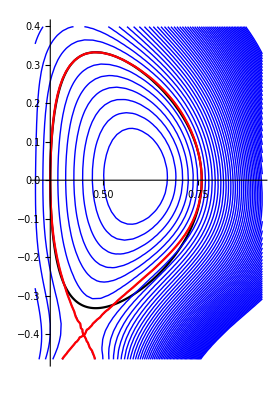

geometry.pdf

geometry.json

{A→0,R_0→173.259,alpha→0.05,c→{0.0735011,-0.0866242,-0.146393,-0.0763124,0.0903179,-0.0915754,-0.00389228,0.0427189,0.227555,-0.130472,-0.0300697,0.00421267},elongation→1.75,equilibrium→solovev,inverseaspectratio→0.410714,psip_max→0,psip_max_cut→5,psip_max_lim→0.2,psip_min→-6,qampl→1,rk4eps→0.00001,triangularity→0.47}

```mathematica
If[Device=="FRC",
Subscript[R, ph]=Function[{τ},(Subscript[R, 0h]+Subscript[a, 0h])*Cos[τ]//Evaluate];
Subscript[Z, ph]=Function[{τ},Subscript[R, 0h] κ*Sin[τ]//Evaluate];
Rotate[Show[{
Show[{ParametricPlot[{Subscript[R, ph][τ],Subscript[Z, ph][τ]},{τ,0,2π},PlotStyle->Black]},AspectRatio->Automatic,PlotRange->All],
ContourPlot[{Subscript[ψ, b][R/Subscript[R, 0],Z/Subscript[R, 0]-Subscript[Z, 0]/Subscript[R, 0h],A,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],Subscript[c, 8],Subscript[c, 9],Subscript[c, 10],Subscript[c, 11],Subscript[c, 12]]},{R,-Subscript[R, maxh]*Subscript[ρ, s],Subscript[R, maxh]*Subscript[ρ, s]},{Z,Subscript[Z, minh]*Subscript[ρ, s]+Subscript[Z, 0],Subscript[Z, maxh]*Subscript[ρ, s]+Subscript[Z, 0]},Contours->90,ContourShading->None,ContourStyle->Blue,PerformanceGoal->"Quality"],ContourPlot[{Subscript[ψ, b][R/Subscript[R, 0],Z/Subscript[R, 0]-Subscript[Z, 0]/Subscript[R, 0],A,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],Subscript[c, 8],Subscript[c, 9],Subscript[c, 10],Subscript[c, 11],Subscript[c, 12]]==0},{R,-Subscript[R, maxh]*Subscript[ρ, s],Subscript[R, maxh]*Subscript[ρ, s]},{Z,Subscript[Z, minh]*Subscript[ρ, s]+Subscript[Z, 0],Subscript[Z, maxh]*Subscript[ρ, s]+Subscript[Z, 0]},ContourStyle->Red,PerformanceGoal->"Quality"]},AspectRatio->Automatic],90Degree],
Subscript[R, ph]=Function[{τ},Subscript[R, 0h]+Subscript[a, h]*Cos[τ+α*Sin[τ]]//Evaluate];
Subscript[Z, ph]=Function[{τ},Subscript[a, h]*κ*Sin[τ]//Evaluate];
Show[{Show[{ParametricPlot[{Subscript[R, ph][τ] Subscript[ρ, s],Subscript[Z, ph][τ] Subscript[ρ, s]},{τ,0,2π},PlotStyle->Black]},AspectRatio->Automatic,PlotRange->All,Framed->True],ContourPlot[{Subscript[ψ, b][R/Subscript[R, 0],Z/Subscript[R, 0]-Subscript[Z, 0]/Subscript[R, 0],A,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],Subscript[c, 8],Subscript[c, 9],Subscript[c, 10],Subscript[c, 11],Subscript[c, 12]]},{R,Subscript[R, minh]*Subscript[ρ, s],Subscript[R, maxh]*Subscript[ρ, s]},{Z,Subscript[Z, minh]*Subscript[ρ, s]+Subscript[Z, 0],Subscript[Z, maxh]*Subscript[ρ, s]+Subscript[Z, 0]},Contours->60,ContourShading->None,ContourStyle->Blue,PerformanceGoal->"Quality"],ContourPlot[{Subscript[ψ, b][R/Subscript[R, 0],Z/Subscript[R, 0]-Subscript[Z, 0]/Subscript[R, 0],A,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],Subscript[c, 8],Subscript[c, 9],Subscript[c, 10],Subscript[c, 11],Subscript[c, 12]]==0},{R,Subscript[R, minh]*Subscript[ρ, s],Subscript[R, maxh]*Subscript[ρ, s]},{Z,Subscript[Z, minh]*Subscript[ρ, s]+Subscript[Z, 0],Subscript[Z, maxh]*Subscript[ρ, s]+Subscript[Z, 0]},ContourStyle->Red,PerformanceGoal->"Quality"]},AspectRatio->Automatic,PlotRange->All,Framed->True],Framed->True]
Export["geometry.pdf",%]
Export["geometry.json",{"A"->A,"R_0"->Subscript[R, 0h],"alpha"->0.05,"c"->N[{Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6],Subscript[c, 7],Subscript[c, 8],Subscript[c, 9],Subscript[c, 10],Subscript[c, 11],Subscript[c, 12]},17],"elongation"->κ,"equilibrium"->"solovev","inverseaspectratio"->ϵ,"psip_max"->0,"psip_max_cut"->5,"psip_max_lim"->0.2,"psip_min"->-6,"qampl"->1,"rk4eps"->0.00001,"triangularity"->δ}]
Import["/home/markus/Documents/Phd/MyFeltor/inc/geometries/COMPASS/geom.json"]
```